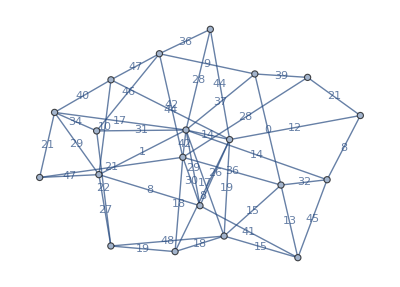

```mathematica
G=RandomGraph[{20,48},EdgeWeight->RandomInteger[48,48],EdgeLabels->"EdgeWeight"]
```

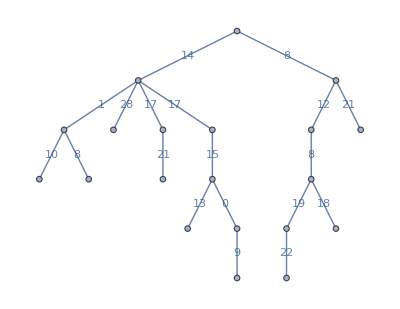

```mathematica
MST=FindSpanningTree[G]
```

```mathematica
oddVertices=Select[VertexList[MST],OddQ[VertexDegree[MST,#]]&]
```

{1,2,3,4,5,6,8,9,10,12,13,14,18,19}

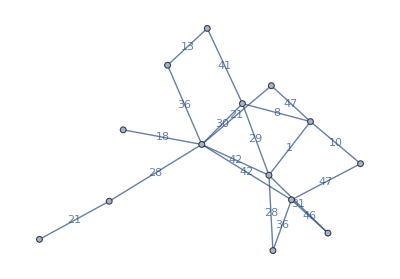

```mathematica
Subgraph[G,oddVertices]
```

```mathematica
minimumCostPerfectMatching=FindIndependentEdgeSet[Subgraph[G,oddVertices]]
```

{1<->9,2<->3,4<->6,5<->10,13<->14,18<->19}

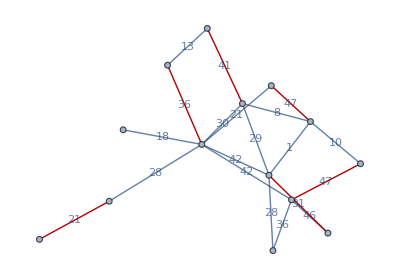

```mathematica
HighlightGraph[Subgraph[G,oddVertices],FindIndependentEdgeSet[Subgraph[G,oddVertices]]]
```

```mathematica
Flatten[EdgeList/@{MST,minimumCostPerfectMatching}]
```

{1<->5,1<->11,2<->8,3<->6,3<->18,3<->19,4<->9,4<->15,5<->8,6<->10,7<->14,7<->18,8<->18,9<->13,11<->15,12<->17,14<->17,14<->20,16<->20,1<->8,3<->10,4<->16,5<->6,7<->11,9<->13,14<->20}

```mathematica
Graph[Flatten[EdgeList/@{MST,minimumCostPerfectMatching}]]
```

-Graphics-

```mathematica
EulerianGraphQ[Graph[Flatten[EdgeList/@{MST,minimumCostPerfectMatching}]]]
```

False

```mathematica
Intersection[EdgeList/@{MST,minimumCostPerfectMatching}]
```

{{1<->8,3<->10,4<->16,5<->6,7<->11,9<->13,14<->20},{1<->5,1<->11,2<->8,3<->6,3<->18,3<->19,4<->9,4<->15,5<->8,6<->10,7<->14,7<->18,8<->18,9<->13,11<->15,12<->17,14<->17,14<->20,16<->20}}

```mathematica
AssociationMap[EulerianGraphQ@GraphProduct[MST,minimumCostPerfectMatching,#]&,{"Cartesian","Conormal","Lexicographical","Normal","Rooted","Tensor"}]
```

<|Cartesian→False,Conormal→False,Lexicographical→False,Normal→False,Rooted→False,Tensor→False|>

```mathematica
AssociationMap[EulerianGraphQ@#[MST,minimumCostPerfectMatching]&,{GraphUnion,GraphSum,GraphJoin,GraphDisjointUnion,GraphIntersection,GraphDifference}]
```

<|GraphUnion→False,GraphSum→False,GraphJoin→False,GraphDisjointUnion→False,GraphIntersection→False,GraphDifference→False|>

```mathematica
Intersection[EdgeList[MST],EdgeList[minimumCostPerfectMatching]]
```

{9<->13,14<->20}

```mathematica
Union[EdgeList[MST],EdgeList[minimumCostPerfectMatching]]
```

{1<->5,1<->8,1<->11,2<->8,3<->6,3<->10,3<->18,3<->19,4<->9,4<->15,4<->16,5<->6,5<->8,6<->10,7<->11,7<->14,7<->18,8<->18,9<->13,11<->15,12<->17,14<->17,14<->20,16<->20}

```mathematica
Graph@Join[EdgeList[MST],EdgeList[minimumCostPerfectMatching]]
```

-Graphics-

```mathematica
VertexDegree@Graph[Join[EdgeList[MST],{1<->11,3<->6,4<->9,5<->8,6<->10,7<->14,9<->13,16<->20}]]
```

{3,3,3,1,4,4,4,3,1,3,4,2,2,3,4,2,1,2,3,2}

```mathematica
Names["*Cover*"]
```

{ColorCoverage,EdgeCoverQ,FindEdgeCover,FindVertexCover,VertexCoverQ}

```mathematica
FindVertexCover[Subgraph[G,oddVertices]]
```

{1,3,4,5,7,10,13,20}

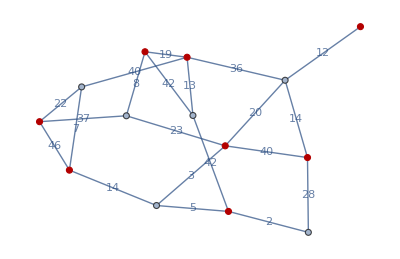

```mathematica
HighlightGraph[Graph[{1,3,4,5,6,7,8,9,10,11,13,14,16,20},{Null,SparseArray[Automatic,{14,14},0,{1,{{0,3,6,9,13,16,20,23,27,30,33,34,37,39,42},{{4},{7},{10},{5},{9},{12},{6},{8},{13},{1},{5},{7},{8},{2},{4},{9},{3},{8},{10},{12},{1},{4},{14},{3},{4},{6},{11},{2},{5},{10},{1},{6},{9},{8},{2},{6},{14},{3},{14},{7},{12},{13}}},Pattern}]},{EdgeLabels->{"EdgeWeight"},EdgeWeight->{19,42,8,7,46,14,40,14,28,40,13,36,22,20,23,3,42,12,37,5,2}}],{1,3,4,5,7,10,13,20}]
```

```mathematica
FindEdgeCover[Subgraph[G,oddVertices]]
```

{1<->11,3<->6,4<->9,5<->8,6<->10,7<->14,9<->13,16<->20}

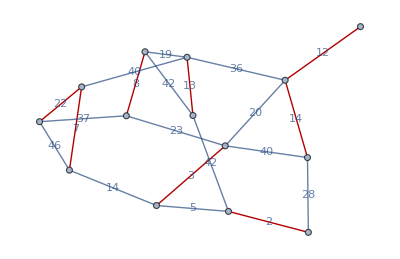

```mathematica
HighlightGraph[Graph[{1,3,4,5,6,7,8,9,10,11,13,14,16,20},{Null,SparseArray[Automatic,{14,14},0,{1,{{0,3,6,9,13,16,20,23,27,30,33,34,37,39,42},{{4},{7},{10},{5},{9},{12},{6},{8},{13},{1},{5},{7},{8},{2},{4},{9},{3},{8},{10},{12},{1},{4},{14},{3},{4},{6},{11},{2},{5},{10},{1},{6},{9},{8},{2},{6},{14},{3},{14},{7},{12},{13}}},Pattern}]},{EdgeLabels->{"EdgeWeight"},EdgeWeight->{19,42,8,7,46,14,40,14,28,40,13,36,22,20,23,3,42,12,37,5,2}}],{1<->11,3<->6,4<->9,5<->8,6<->10,7<->14,9<->13,16<->20}]
```

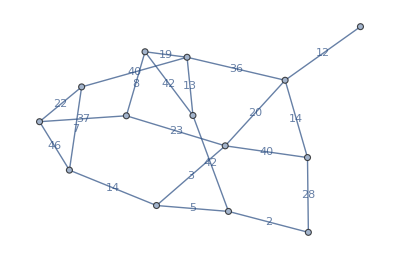

```mathematica
Subgraph[G,oddVertices]
```

```mathematica
VertexCount@Subgraph[G,oddVertices]
```

14

```mathematica
Join[EdgeList@FindIndependentEdgeSet[Subgraph[G,oddVertices]],EdgeList@MST]
```

{1<->8,3<->10,4<->16,5<->6,7<->11,9<->13,14<->20,1<->5,1<->11,2<->8,3<->6,3<->18,3<->19,4<->9,4<->15,5<->8,6<->10,7<->14,7<->18,8<->18,9<->13,11<->15,12<->17,14<->17,14<->20,16<->20}

```mathematica
Graph@Join[EdgeList@FindIndependentEdgeSet[Subgraph[G,oddVertices]],EdgeList@MST]
```

-Graphics-

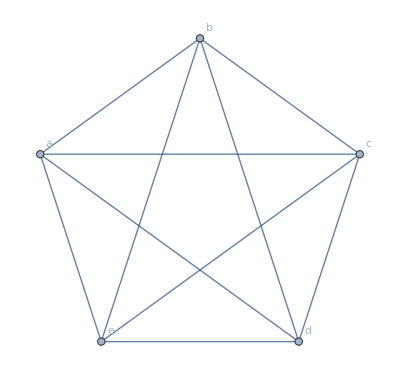

```mathematica
Graph[{a,b,c,d,e},{a<->b,b<->c,c<->d,d<->a,a<->e,a<->c,b<->e,c<->e,d<->e,b<->d},VertexLabels->Automatic]
```

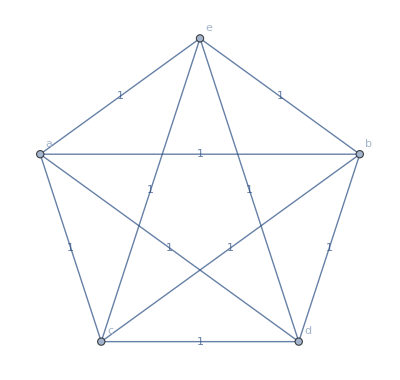

```mathematica
G=Graph[UndirectedEdge@@@{{a,e,2},{a,b,1},{a,d,1},{a,c,1},{b,e,1},{b,c,1},{b,d,2},{e,c,1},{d,e,1},{d,c,1}},EdgeLabels->"EdgeWeight",VertexLabels->Automatic]
```

```mathematica
UndirectedEdge@@@{{a,e,2},{a,b,1},{a,d,1},{a,c,1},{b,e,1},{b,c,1},{b,d,2},{e,c,1},{d,e,1},{d,c,1}}
```

{ae2,ab1,ad1,ac1,be1,bc1,bd2,ec1,de1,dc1}

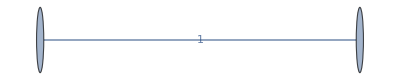

```mathematica
Graph[{a,e},{ae2},EdgeLabels->"EdgeWeight"]
```

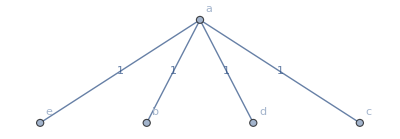

```mathematica
minimumSpanningTree=FindSpanningTree[G]
```

```mathematica
Select[VertexList[]]
```

```mathematica
G=RandomGraph[{20,48},EdgeWeight->RandomInteger[48,48],EdgeLabels->"EdgeWeight"]
```

-Graphics-

```mathematica
T=FindSpanningTree[G]
```

-Graphics-

```mathematica
oddVertices=Select[VertexList[T],OddQ[VertexDegree[T,#]]&]
```

{1,2,3,4,5,6,8,9,10,12,13,14,18,19}

```mathematica
FindIndependentEdgeSet@Subgraph[G,oddVertices]
```

{1<->9,2<->3,4<->6,5<->10,13<->14,18<->19}

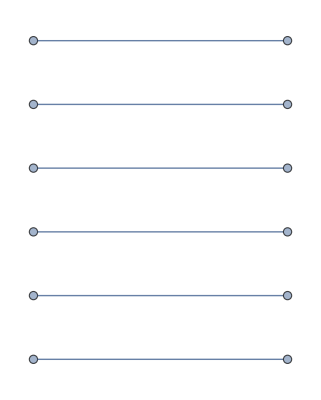

```mathematica
minimumCostPerfectMatching=Graph@FindIndependentEdgeSet[Subgraph[G,oddVertices]]
```

```mathematica
Join[EdgeList[MST],FindIndependentEdgeSet@Subgraph[G,oddVertices]]
```

{1<->20,2<->15,3<->6,3<->9,3<->10,4<->11,5<->18,6<->8,6<->15,6<->16,6<->17,7<->12,7<->13,11<->12,12<->19,13<->14,13<->17,16<->18,18<->20,1<->9,2<->3,4<->6,5<->10,13<->14,18<->19}

```mathematica
Graph[%173]
```

-Graphics-

```mathematica
Graph[Join[EdgeList[MST],EdgeList[minimumCostPerfectMatching]]]
```

-Graphics-

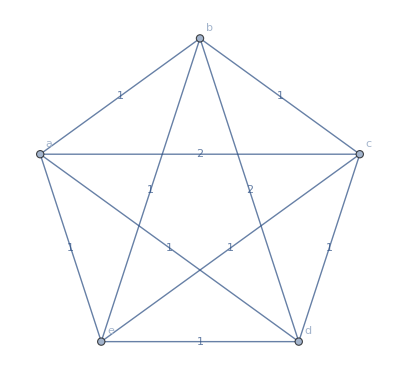

```mathematica
G=Graph[{a,b,c,d,e},{a<->b,a<->e,a<->d,a<->c,b<->c,b<->e,c<->e,c<->d,d<->e,b<->d},VertexLabels->Automatic,EdgeWeight->Thread[{a<->b,a<->e,a<->d,a<->c,b<->c,b<->e,c<->e,c<->d,d<->e,b<->d}->{1,1,1,2,1,1,1,1,1,2}],EdgeLabels->"EdgeWeight"]
```

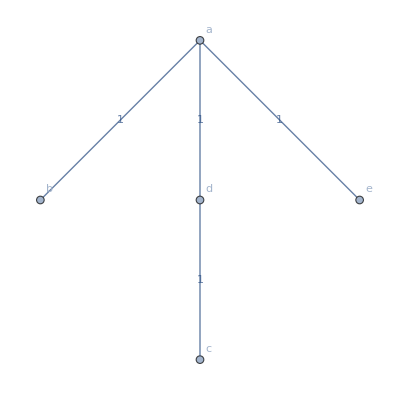

```mathematica
T=FindSpanningTree[G]
```

```mathematica
Select[VertexList[T],OddQ[VertexDegree[T,#]]&]
```

{a,b,c,e}

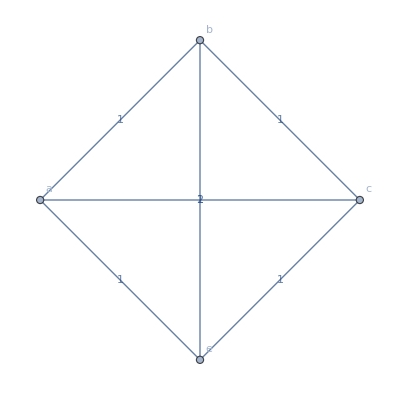

```mathematica
Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]
```

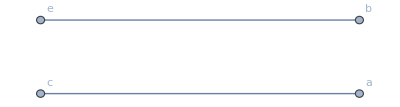

```mathematica
Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic]
```

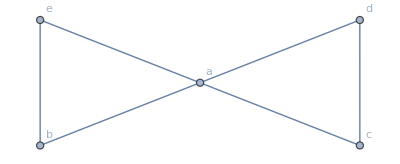

```mathematica
GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]
```

```mathematica
FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]]
```

{{a<->d,d<->c,c<->a,a<->e,e<->b,b<->a}}

```mathematica
Flatten@Map[{First[#],Last[#]}&,FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]],{2}]
```

{a,d,d,c,c,a,a,e,e,b,b,a}

```mathematica
DeleteDuplicates@Partition[RotateRight[Flatten@Map[{First[#],Last[#]}&,FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]],{2}]],2]
```

{{a,a},{d,d},{c,c},{e,e},{b,b}}

```mathematica
RotateLeft[Flatten[DeleteDuplicates@Partition[RotateRight[Flatten@Map[{First[#],Last[#]}&,FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]],{2}]],2]]]
```

{a,d,d,c,c,e,e,b,b,a}

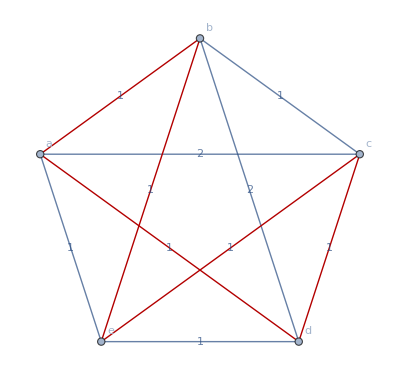

```mathematica
HighlightGraph[G,UndirectedEdge@@@Partition[RotateLeft[Flatten[DeleteDuplicates@Partition[RotateRight[Flatten@Map[{First[#],Last[#]}&,FindEulerianCycle[GraphSum[Graph[FindIndependentEdgeSet[Subgraph[G,Select[VertexList[T],OddQ[VertexDegree[T,#]]&]]],VertexLabels->Automatic],T,VertexLabels->Automatic]],{2}]],2]]],2]]
```

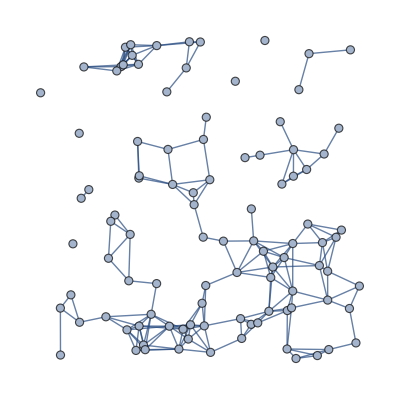
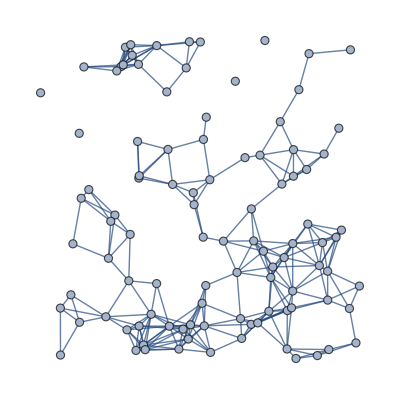
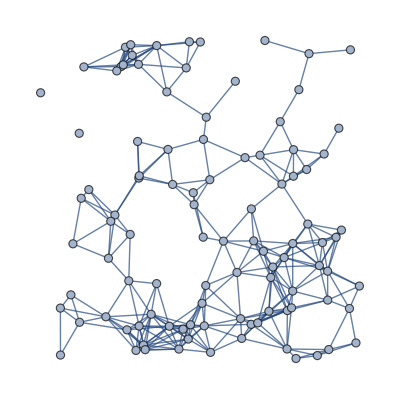
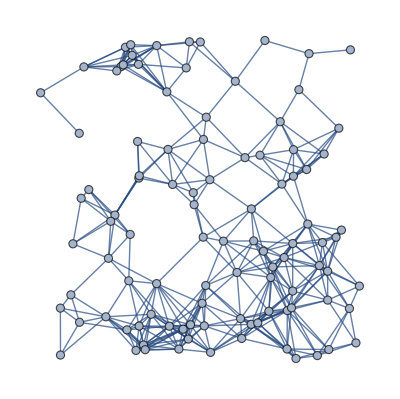

```mathematica
Table[SeedRandom[4];RandomGraph[SpatialGraphDistribution[100,0.15,DistanceFunction->(Norm[#2-#1,p]&)]],{p,{1,1.5,2,∞}}]
```

```mathematica
InputForm@First[Table[SeedRandom[4];RandomGraph[SpatialGraphDistribution[20,0.15,DistanceFunction->(Norm[#2-#1,p]&)]],{p,{1,1.5,2,∞}}]]
```

Graph[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20}, {UndirectedEdge[2, 15], UndirectedEdge[3, 13], 
  UndirectedEdge[5, 7], UndirectedEdge[5, 17], UndirectedEdge[6, 17], UndirectedEdge[6, 7], UndirectedEdge[6, 14], UndirectedEdge[8, 10], 
  UndirectedEdge[8, 17], UndirectedEdge[8, 14], UndirectedEdge[14, 17]}, 
 {VertexCoordinates -> {{0.3113761158140893, 0.5660040004070195}, {0.6271553449468614, 0.1293134122192845}, {0.7916359845436349, 
   0.6544086319924736}, {0.10678317093971867, 0.3618092618656048}, {0.8720116193879339, 0.2942152063498533}, {0.7891131909779359, 
   0.2150457540715247}, {0.8977821251253189, 0.1869049154486111}, {0.667945907017713, 0.3709102733463625}, {0.21709424438161395, 
   0.31685194205855693}, {0.5740753897085578, 0.3701079839305972}, {0.5207801280123863, 0.7552755042870611}, {0.8083408549549509, 
   0.8408666113487815}, {0.7504516274005462, 0.7413136904674589}, {0.7893358574823457, 0.36270511873962796}, {0.6601124044033353, 
   0.11155605858385464}, {0.9855017648459508, 0.05381918052501655}, {0.727366061794789, 0.28978015056563766}, {0.3982819362955765, 
   0.834048367712916}, {0.4718343966872771, 0.11025883954632154}, {0.3666080769292668, 0.2381734794494419}}}]